```mathematica
Remove["Global`*"];
Unprotect[In,Out];
Clear[In,Out];
Off[General::spell1]
<<VariationalMethods`
```

```mathematica
ℒ =1/2(ⅇ^(2 Subscript[F, 1][r[τ]])/H[r[τ]] r'[τ]^2+ⅇ^(2 Subscript[F, 2][r[τ]])r[τ]^2(ϕ'[τ]-W[r[τ]]/r[τ] t'[τ])^2-ⅇ^(2 Subscript[F, 0][r[τ]])H[r[τ]] t'[τ]^2);
```

```mathematica
FirstIntegrals[ℒ,{ϕ[τ],t[τ],r[τ]},τ];
ϕFirstIntegral=FullSimplify[-FirstIntegral[ϕ] /. %];
tFirstIntegral=FullSimplify[FirstIntegral[t] /. %%];
```

```mathematica
solution =FullSimplify[Solve[{ϕFirstIntegral == L, tFirstIntegral == En}, {t'[τ] , ϕ'[τ]}]][[1]];
```

```mathematica
potential=Simplify[Solve[(ℒ/.solution /. r'[τ]^2->X)==0,X][[1]]];
V[r_] = Factor[Simplify[X /. potential /. r[τ]-> r]]
derV[r_] = FullSimplify[D[V[r],r] /. potential];
```

(ⅇ^(-2 F_0[r]-2 F_1[r]-2 F_2[r]) (ⅇ^(2 F_2[r]) En^2 r^2-ⅇ^(2 F_0[r]) L^2 H[r]-2 ⅇ^(2 F_2[r]) En L r W[r]+ⅇ^(2 F_2[r]) L^2 W[r]^2))/r^2

```mathematica
Vplus[r_] = Simplify[(X /. Solve[V[r]==0/.En->X,X][[2]])/L]
Vminus[r_] = Simplify[(X /. Solve[V[r]==0/.En->X,X][[1]])/L]
```

(ⅇ^(F_0[r]-F_2[r]) √H[r]+W[r])/r

(-ⅇ^(F_0[r]-F_2[r]) √H[r]+W[r])/r

```mathematica
(* 1  2   3   4  5  6   7*)
(* nr,w,alpha,c1,c2,c3,rh*)
conf=ReadList["res.txt",Number,RecordLists->True];

 
nr=conf[[1]][[1]];
V= conf[[1]][[2]];
w= conf[[1]][[3]];
rh= conf[[1]][[4]];
gr=ReadList["gridx.dat",{Number}];


lgr=Length[gr];
nx=lgr;

listar=Table[gr[[k]][[1]],{k,1,lgr}] ;
listalogr=Table[Log[10,gr[[k]][[1]]],{k,1,lgr}];



dat=ReadList["f-tPi2.txt",Number,RecordLists->True];
lung1=Length[dat] ;

 nF1=Table[dat[[i]][[2]],{i,1,lung1}];
 nF2=Table[dat[[i]][[3]],{i,1,lung1}];
nF0=Table[dat[[i]][[4]],{i,1,lung1}];
nZ=Table[dat[[i]][[5]],{i,1,lung1}];
nW=Table[dat[[i]][[6]],{i,1,lung1}];

order=3;
Subscript[F, 1]=ListInterpolation[nF1,{listar},InterpolationOrder->order];
Subscript[F, 2]=ListInterpolation[nF2,{listar},InterpolationOrder->order];
Subscript[F, 0]=ListInterpolation[nF0,{listar},InterpolationOrder->order];
Z=ListInterpolation[nZ,{listar},InterpolationOrder->order];
W=ListInterpolation[nW,{listar},InterpolationOrder->order];
```

```mathematica
(* Here I compute first derivatives *)
 
dat=ReadList["fx-tPi2.txt",Number,RecordLists->True];
lung1=Length[dat] ;

 nF1x=Table[dat[[i]][[2]],{i,1,lung1}];
 nF2x=Table[dat[[i]][[3]],{i,1,lung1}];
nF0x=Table[dat[[i]][[4]],{i,1,lung1}];
nZx=Table[dat[[i]][[5]],{i,1,lung1}];
nWx=Table[dat[[i]][[6]],{i,1,lung1}];

order=3;
Subscript[F, 1]'=ListInterpolation[1/(1+listar)^2 nF1x,{listar},InterpolationOrder->order];
Subscript[F, 2]'=ListInterpolation[1/(1+listar)^2 nF2x,{listar},InterpolationOrder->order];
Subscript[F, 0]'=ListInterpolation[1/(1+listar)^2 nF0x,{listar},InterpolationOrder->order];
Z'=ListInterpolation[1/(1+listar)^2 nZx,{listar},InterpolationOrder->order];
W'=ListInterpolation[1/(1+listar)^2 nWx,{listar},InterpolationOrder->order];
```

```mathematica
derVplus[r_]=FullSimplify[D[Vplus[r],r]];
derVminus[r_]=FullSimplify[D[Vminus[r],r]];
```

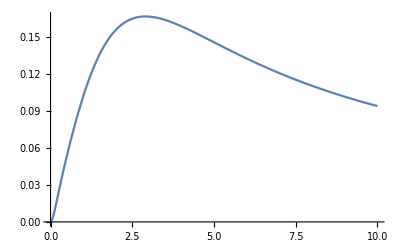

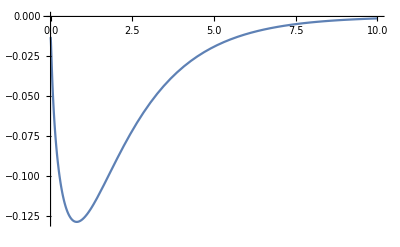

{-0.128664,{r→0.800689}}

```mathematica
Plot[W[r],{r,0,10}]
Plot[Z[r],{r,0,10}]
NMinimize[{Z[r],r>0},r]
```

```mathematica
H[r_]:=1-rh/r;
```

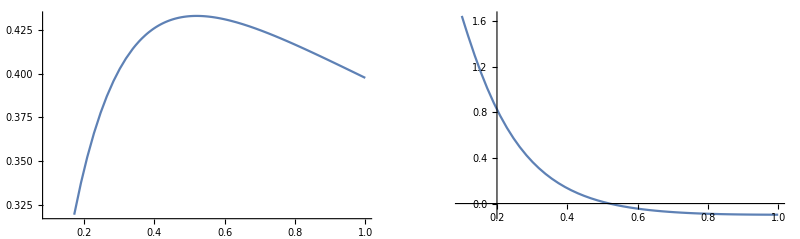

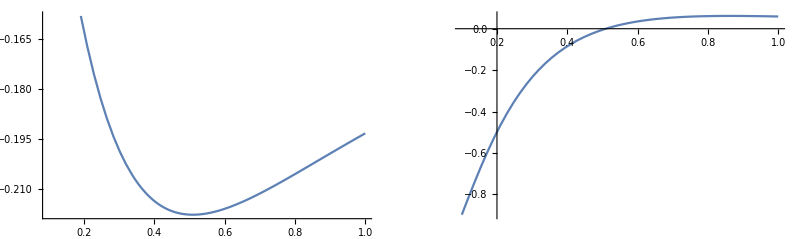

```mathematica
rMin=0.1;rMax=1;
GraphicsRow[{Plot[Vplus[r],{r,rMin,rMax}]
,Plot[derVplus[r],{r,rMin,rMax}]}]
GraphicsRow[{Plot[Vminus[r],{r,rMin,rMax}]
,Plot[derVminus[r],{r,rMin,rMax}]}]
```

```mathematica
rPH1=FindRoot[(derVplus[r])==0,{r,0.5}]
rPH2=FindRoot[(derVminus[r])==0,{r,0.5}]
```

{r→0.520295}

{r→0.509535}

```mathematica
(*output={{w,r/.rPH1,r/.rPH2}};
Export["light-rings.dat",output,"Table"];*)
```